-0.000586394

0.111992

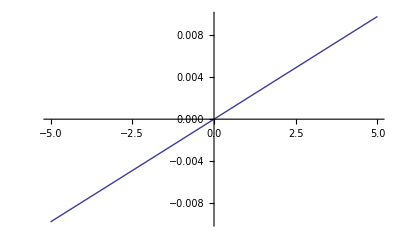

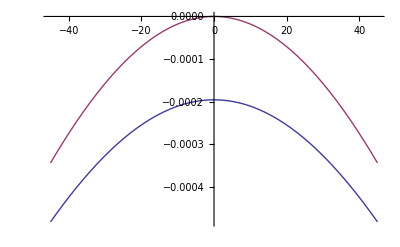

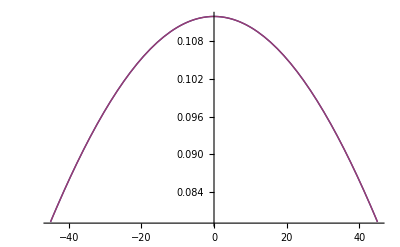

```mathematica
Clear[χ,θ,ω]
q:=(4π Sin[θ])/λ
qx[χ_]:=q Cos[θ]Sin[χ*π/180]
qy[χ_,ω_]:=q(-Sin[θ]Cos[ω]+Cos[θ]Cos[χ*π/180]Sin[ω])
qz[χ_,ω_]:=q(Sin[θ]Sin[ω]+Cos[θ]Cos[χ*π/180]Cos[ω])
θ=0.6*π/180;
λ=1.175;
w=3;
qy[0,0.3*π/180]
qz[0,0.3*π/180]
Plot[qx[χ],{χ,-5,5}]
Plot[{qy[χ,0.5*π/180],qy[χ,0.6*π/180]},{χ,-45,45}]
Plot[{qz[χ,0.5*π/180],qz[χ,0.6*π/180]},{χ,-45,45}]
```